# SWIRP Diffraction Grating

Three Dimensional Grating Equation (Function)

```mathematica
GratingEq3D[λ_,nI_,nII_,θ_,ϕ_,i_,d_]:=Module[{ko,kxo,kyo,kIzo,kinc,kxi,kIzi,kIIzi,ψi },
ko=2*π/λ;
kxo=ko*nI*Sin[θ]*Cos[ϕ];
kyo=ko*nI*Sin[θ]*Sin[ϕ];
kIzo=ko*nI*Cos[θ];
kinc={kxo,kyo,kIzo};
kxi=ko*(nI*Sin[θ]*Cos[ϕ](*-i*)+i*λ/d);
If[Sqrt[kxi^2+kyo^2]≤ko*nI,
kIzi=Sqrt[(ko*nI)^2-(kxi^2+kyo^2)],
kIzi=-I*Sqrt[(kxi^2+kyo^2)-(ko*nI)^2]];
If[Sqrt[kxi^2+kyo^2]≤ko*nII,
kIIzi=Sqrt[(ko*nII)^2-(kxi^2+kyo^2)],
kIIzi=-I*Sqrt[(kxi^2+kyo^2)-(ko*nII)^2]];
Chop[
{(*reflect*)Normalize[{kxi,kyo,-kIzi}],
(*transmit*)Normalize[{kxi,kyo,kIIzi}]}
]
]
```

Multiple Order Plot

### Set-Up

```mathematica
mmm=.045;(*scaling diffracted ray color*)
θin=0 Degree;ϕin=50 Degree;
kin={Sin[θin]*Cos[ϕin],Sin[θin]*Sin[ϕin],Cos[θin]}; (*incident angle*)
```

```mathematica
(□_□)_□
```

```mathematica
λ=12.5;
ni=1;nt=1;
period=30 (*μm*);
```

```mathematica
xx=10;(*+/- xx plotrange*)
al=1.35;(*black axis length*)
ch=0.02;(*small cylinder thickness*)
opac=.2;(*opacity for green sphere*)
tck=0.005;(*thickness of lines*)
tko=0.02;(*thickness of diffracted lines*)
ahead=.01;(*arrowheads size*)
psz=0.01;(*small cylinder radius*)
```

### Multiple Order Plot

```mathematica
plot2=
Graphics3D[{Specularity[.8],
Darker[Gray],Opacity[1],Thickness[0.02],Table[Tube[Line[{{x,-Sqrt[1-x^2]+0.1,0},{x,Sqrt[1-x^2]-0.1,0}}],0.02],{x,-1,1,0.05}],
Opacity[opac],
(* incident*)Blue,Opacity[1],Arrowheads[ahead],Arrow[Tube[{(0.7+1)*kin,1.3*kin},tko+0.01]],Tube[{(1+0.8)*kin,{0,0,0}},tko+0.01],EdgeForm[{}],Arrowheads[ahead],
Table[
(* diffracted*) { Lighter[Blue],
Thickness[tko],
Arrow[Tube[{{0,0,0},-{1,1,-1}*GratingEq3D[λ,ni,nt,θin,ϕin,order,period][[1]]{1,1,-1}},tko]]
},{order,{-1,0,1}}]
},PlotRange->{{-xx,xx+0.1},{-xx,xx},{-0.1,1.8}},ViewVertical->{0,0,1},ViewPoint->(*{0,0,10}*){5,-10,2},Axes->False,AxesLabel->{"x","y","z"},ViewAngle->5°,Boxed->False,ImageSize->300*3]
```

-Graphics3D-

Dispersion Plot

```mathematica
spa=0.08;
tck=0.005;(*thickness of lines*)
tko=0.02;(*thickness of diffracted lines*)
ahead=.05;(*arrowheads size*)
psz=0.03;(*small cylinder radius*)
```

```mathematica
plot1=
Graphics3D[{Specularity[.3],
(* incident*)GrayLevel[0.8],Opacity[0.8],Arrowheads[ahead+0.04],Arrow[Tube[{1.8kin,1.3*kin},tko+0.01]],Tube[{1.8*kin,{0,0,0}},tko+0.01],EdgeForm[{}],Opacity[1],
Table[
(* diffracted*) { Lighter[Blue],
Thickness[tko],Arrowheads[0.03],
Arrow[Tube[{{0,0,0},-{1,1,-1}*GratingEq3D[(*λ*)8.5,ni,nt,θin,ϕin,order,period][[1]]*{1,1,-1}},tko-0.01]]
},{order,{-1,0,1}}],
Table[
(* diffracted*) { Lighter[Green],
Thickness[tko],Arrowheads[0.03],
Arrow[Tube[{{0,0,0},Normalize[-{1,1,-1}*GratingEq3D[(*λ*)9.5,ni,nt,θin,ϕin,order,period][[1]]*{1,1,-1}(*{1-spa,1,-1}*)]},tko-0.01]]
},{order,{-1,0,1}}],
Table[
(* diffracted*) { Lighter[Orange],
Thickness[tko],Arrowheads[0.03],
Arrow[Tube[{{0,0,0},Normalize[-{1,1,-1}*GratingEq3D[(*λ*)10.5,ni,nt,θin,ϕin,order,period][[1]]*{1,1,-1}(*{1-2*spa,1,-1}*)]},tko-0.01]]
},{order,{-1,0,1}}],
Table[
(* diffracted*) { Lighter[Red],
Thickness[tko],Arrowheads[0.03],
Arrow[Tube[{{0,0,0},Normalize[-{1,1,-1}*GratingEq3D[(*λ*)11.5,ni,nt,θin,ϕin,order,period][[1]]*{1,1,-1}(*{1-3*spa,1,-1}*)]},tko-0.01]]
},{order,{-1,0,1}}],

Table[
(* diffracted*) { GrayLevel[0.8],
Thickness[tko],Arrowheads[0.03],
Arrow[Tube[{{0,0,0},-{1,1,-1}*GratingEq3D[(*λ*)12.5,ni,nt,θin,ϕin,order,period][[1]]*{1,1,-1}},tko-0.01]]
},{order,{-1,0,1}}],
Specularity[.8],
Darker[Gray],Opacity[1],Thickness[0.02],Table[Tube[Line[{{x,-Sqrt[1-x^2]+0.1,0},{x,Sqrt[1-x^2]-0.1,0}}],0.02],{x,-1,1,0.05}],
Opacity[opac],
},PlotRange->All(*{{-xx,xx+0.1},{-xx,xx},{-xx,xx-0.1}}*),ViewVertical->{0,0,1},ViewAngle->4.7°,ViewPoint->(*{0,0,10}*){5,-10,2},Axes->False,AxesLabel->{"x","y","z"},Boxed->False,ImageSize->100*10]
```

-Graphics3D-

```mathematica
x=GratingEq3D[(*λ*)8.5,ni,nt,θin,ϕin,1,period][[1]][[1]];
z=GratingEq3D[(*λ*)8.5,ni,nt,θin,ϕin,1,period][[1]][[3]];
```

```mathematica
Tan[x/z]
```

-0.304347

```mathematica
ang85=-0.304346;
ang12=-0.4933;

ang12-ang85
```

-0.188954

#### Blaze Angle

```mathematica
λblaze=10;
period=30(*μm*);
θB1=ArcSin[1 *λblaze/(2*period)];
θB2=π/2.-θB1;
{θB1,θB2}/°;
numberLayer=30;
```

```mathematica
config`rayID=1; (* starting value for rayID *)
nκ=RefractiveIndex["PalikMetal","Cu",0.8]⟦2,1⟧
numOrders=(*50*)100;
orderRange=Range[0,1];
orderLit=-1;
```

0.249913+5.03371 ⅈ

#### Grating Efficiency Calculation

```mathematica
Monitor[effTab2=(*ParallelTable*)Table[(Print[offst,"  "<>ToString[offst],DateString[Date[]]];
offData[offst]=Table[Prepend[Module[{(*  *)},
aoi=ArcCos[(2 √(2 period^4 Cos[offst/2]^4-orderLit^2 period^2 λvary^2 Cos[offst/2]^4+2 period^4 Cos[offst/2]^4 Cos[offst])-orderLit period λvary Sin[offst])/(2 (period^2+period^2 Cos[offst]))];
ki={Sin[aoi],0,Cos[aoi]};
(* optical system, first surface is grating, second and final is dummy*)
opticalSystem={
(*CreateBlazedGratingSurface calculates the geometry for the blazed grating*)
CreateTriangularGratingSurface[nκ,period,{"ANGLE",θB1,θB2},numberLayer,
{sys`surfID->1 ,sys`material1->"Air",sys`material2->"Air",sys`mode->{"Reflect"},
sys`coating`RCWA`xLocal(*direction containing grating repetitions*)->Normalize[{1,0,0}],
sys`coating`RCWA`ordersCalculate->numOrders,sys`coating`RCWA`ordersReturned->orderRange,
sys`aperture->(Norm[{#1,#2}-{0,0}]<5.00&)}],
(*a detector surface*)
CreateSurface[ sys`v->{0,0,-5},sys`shape`curv->1/5,sys`shape`conicK->0,sys`aperture->(Norm[{#1,#2}-{0,0}]<5.00&),sys`surfID->2,sys`material1->"Air",sys`material2->"Air",sys`mode->{"Refract"}]};
surNormal=opticalSystem[[1,6]]; (* note hardwired value *)
angleIncidence=VectorAngle[ki,surNormal];
(*basis vectors*)
{sPolarization,pPolarization}=CreateSP[surNormal,ki];
raySet={CreateRay[ray`k->ki,ray`r->-2*ki,ray`λ->λvary]};
abtime=AbsoluteTiming[(Print[DateString[Date[]],"  ",λvary];
output=TraceRays[raySet,opticalSystem])
][[1]];
(* Select real diffracted ray segments, not evanescent segments *)
orders=Select[output,#[[ray`surfaceID]] ==1&&#⟦ray`status⟧==1&];
(* pick out order, propagation vectors, angle of diffraction, projection factors, PRT *)
values={ ToExpression[StringTake[#[[ray`modeLabel]][[1]],-1]] (* take string to integer *),#[[ray`k]],VectorAngle[#[[ray`k]],-surNormal ],Cos[VectorAngle[#[[ray`k]],-surNormal ]]/Cos[angleIncidence],#[[ray`PRTCumulative]]} & /@ orders ;
(* return order, s Efficiency, p efficiency, angle of diffraction, angular dispersion, PRT  *)
efficiencies={#[[1]],Chop[#[[4]]*(#[[5]].sPolarization).Conjugate[#[[5]].sPolarization]] (*insignificant imaginary part *) ,Chop[#[[4]]*(#[[5]].pPolarization).Conjugate[#[[5]].pPolarization]],#[[3]],#[[1]]/Sqrt[period^2 -(-#[[1]] λvary+period Sin[angleIncidence])^2]/1000, #[[5]]} & /@ values
]
,{λvary,period,θB1,θB2,angleIncidence}],
{λvary,8.5,12.5,.5}];
Export["offdata"<>ToString[Round[10 offst]]<>".wdx",offData[offst]];
offData[offst]
),
{offst,(*-.2*).2,.2,.05}];,offst]
```

0.2  0.2Fri 22 Nov 2019 11:19:56

Fri 22 Nov 2019 11:19:56  8.5

$Aborted

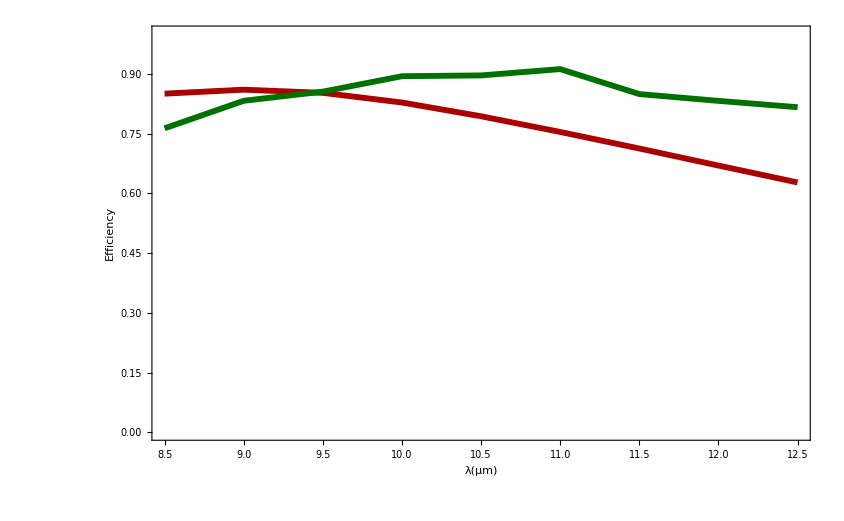

```mathematica
txt=20;
offst=1;
lp[offst]=
ListPlot[
{Table[{effTab2[[offst,qq,1,1]],effTab2[[offst,qq,3,2]]},{qq,Length[effTab2[[1]]]}],
Table[{effTab2[[offst,qq,1,1]],effTab2[[offst,qq,3,3]]},{qq,Length[effTab2[[1]]]}]},
Joined->True,PlotStyle->{Directive[(*Hue[offst/2.]*)Blend[{LightPink,Darker[Red]},offst/Length[effTab2]],Thickness[0.005]],Directive[(*Hue[.5+offst/15.]*)Blend[{Lighter[Lighter[Green]],Darker[Darker[Green]]},offst/Length[effTab2]],Thickness[0.005]]},Axes->False,PlotRange->{All,{0,1}},Frame->True,FrameStyle->Directive[Black,txt-.5], FrameLabel->{Style["λ(μm)",txt],Style["Efficiency",txt]},ImageSize->72*2.5]
```

#### Plot Grating Profile

```mathematica
Subscript[λ, B]=10;
Subscript[θ, B]=ArcSin[Subscript[λ, B]/(2*period)]
Subscript[θ, B]*1.0/Degree
```

ArcSin[1/6]

9.59407

{-6.,10.4645}

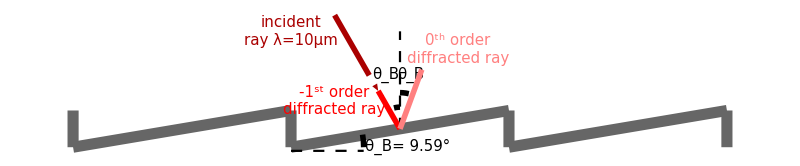

```mathematica
gH=Tan[Subscript[θ, B]]*period;gL=0;perio=period;txS=15;kin={perio(1.3),13}-{perio (1+0.5),0.5 gH}
Magnify[plot9a=Graphics[{Thickness[0.01],GrayLevel[.4],
Line[{{0,gH},{0,gL}}],
Line[{{0,gL},{perio,gH}}],
Line[{{perio,gH},{perio,gL}}],
Line[{{perio,gL},{2 perio,gH}}],
Line[{{2 perio,gH},{2 perio,gL}}],
Line[{{2 perio,gL},{3 perio,gH}}],
Line[{{3 perio,gH},{3 perio,gL}}],
Black,Thickness[0.002],Dashing[0.01],Line[{{perio,gL-.5},{perio+10,gL-.5}}],
Line[{{perio (1+0.5),0.5 gH},{perio (1+0.5),16}}],
Thickness[0.005],Text[Style["θ_B= 9.59°",txS(*,Blue*),FontFamily->"Times"],{perio+16,0}],
Text[Style["θ_B",txS(*,Blue*),FontFamily->"Times"],{perio+13,10}],
Text[Style["θ_B",txS(*,Blue*),FontFamily->"Times"],{perio+16.5,10}],
Text[Style[Column[{"incident","ray λ=10μm"},Center,Spacings->0],txS,FontFamily->"Times",Darker[Red]],{perio,16}],
Text[Style[Column[{"-1^st order","diffracted ray"},Right,Spacings->0],txS,FontFamily->"Times",Red],{perio+6,6.4}],
Text[Style[Column[{"0^th order","diffracted ray"},Left,Spacings->0],txS,FontFamily->"Times",Pink],{perio+23,13.5}],
(*Blue,*)Dashing[1],Circle[{perio,0},10,{0°,10°}],
Circle[{perio (1+0.5),0.5 gH},3,{90°,106°}],
Circle[{perio (1+0.5),0.5 gH},5,{76°,90°}],
Red,Arrow[{{perio (1+0.5),0.5 gH},{perio (1+0.5),0.5 gH}+0.5*kin}],
Darker[Red],Arrow[{{perio (1+0.5),0.5 gH}+1.5*kin,{perio (1+0.5),0.5 gH}+0.5*kin}],
Pink,Arrow[{{perio (1+0.5),0.5 gH},{perio (1+0.4),0.05gH}+1*{-kin[[1]],kin[[2]]}}]
},ImageSize->200*4],1.3]
```

### Determine Necessary Aperture Size

```mathematica
dispersioneq[α_,λ_,d_]:=Module[{m},
m=1;
ArcSin[Sin[α]+m λ/d]];
```

```mathematica
α1=-5 Degree;
spac=30;
dispersionangles=Table[dispersioneq[α1,λ,spac],{λ,{8.5,9.5,10.5,11.5,12.5}}]
```

{0.197458,0.231575,0.265969,0.300688,0.335786}

```mathematica
distance=15;(*mm*)
locations=Table[distance*Tan[dispersionangles[[n]]],{n,{1,2,3,4}}]
```

{3.00098,3.53708,4.08635,4.65136}

```mathematica
locations[[4]]-locations[[1]]
```

1.65038

{-6.,10.4645}

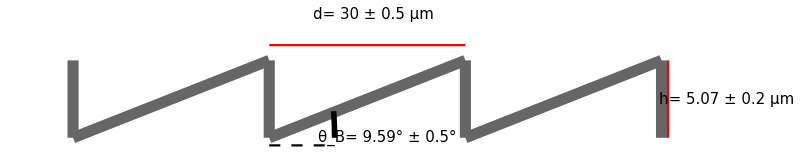

```mathematica
gH=Tan[Subscript[θ, B]]*period;gL=0;perio=period;txS=15;kin={perio(1.3),13}-{perio (1+0.5),0.5 gH}
Magnify[plot9a=Graphics[{Thickness[0.01],GrayLevel[.4],
Line[{{0,gH},{0,gL}}],
Line[{{0,gL},{perio,gH}}],
Line[{{perio,gH},{perio,gL}}],
Line[{{perio,gL},{2 perio,gH}}],
Line[{{2 perio,gH},{2 perio,gL}}],
Line[{{2 perio,gL},{3 perio,gH}}],
Line[{{3 perio,gH},{3 perio,gL}}],
Red,Thickness[0.002],Line[{{perio , gH+1},{2perio ,gH+1}}],
Line[{{3perio +1, gH},{3perio+1 ,gL}}],
Black,Thickness[0.002],Dashing[0.01],Line[{{perio,gL-.5},{perio+10,gL-.5}}],

Thickness[0.005],Text[Style["θ_B= 9.59° ± 0.5°",txS(*,Blue*),FontFamily->"Times"],{perio+18,0}],Text[Style["d= 30 ± 0.5 μm",txS(*,Blue*),FontFamily->"Times"],{perio+16,gH+3}],Text[Style["h= 5.07 ± 0.2 μm",txS(*,Blue*),FontFamily->"Times"],{3perio+10,(gH-gL)/2}],
(*Blue,*)Dashing[1],Circle[{perio,0},10,{0°,10°}],
},ImageSize->200*4],1.3]
```

```mathematica
q
```